eqs = {{(Y_1)'[T]==Y_2[T],(Y_2)'[T]==-Y_1[T]},{Y_1[0]==1,Y_2[0]==0}}

vars = {Y_1[T],Y_2[T]}

time = {T,0,100}

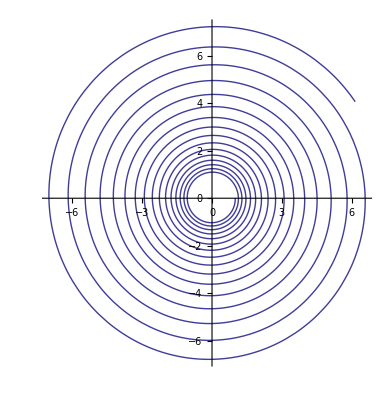

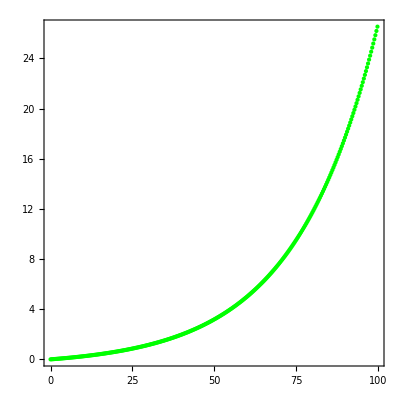

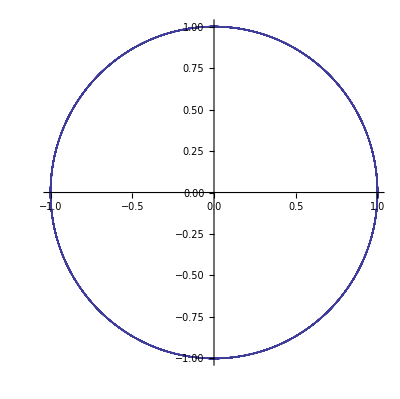

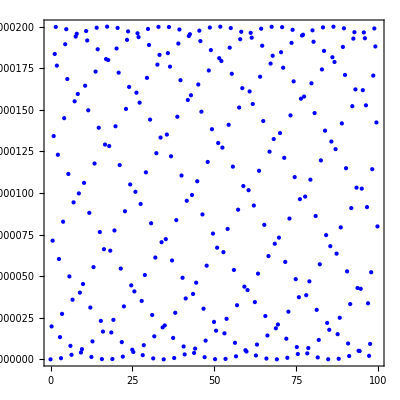

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];

system=GetNDSolveProblem["HarmonicOscillator"];
eqs={system["System"],system["InitialConditions"]};
vars=system["DependentVariables"];
H=system["Invariants"];
time={T,0,100};
step=1/25;

Print["eqs = ", eqs];
Print["vars = ", vars];
Print["time = ", time];

solee=NDSolve[eqs,vars,time,Method->"ExplicitEuler",StartingStepSize->step,MaxSteps->Infinity];

Print[ParametricPlot[Evaluate[vars/.First[solee]],Evaluate[time],PlotPoints->100]];

Print[InvariantErrorPlot[H,vars,T,solee,PlotStyle->Green]];

sol=NDSolve[eqs,vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{Subscript[Y,1][T]}},StartingStepSize->step,MaxSteps->Infinity];

Print[ParametricPlot[Evaluate[vars/.First[sol]],Evaluate[time]]];

Print[InvariantErrorPlot[H,vars,T,sol,PlotStyle->Blue]];
```